## Monte Carlo Playground and Program

Monte Carlo is a method for drawing a set of representative samples from a complex probability distribution. It is powerful because it works on high-dimensional probability distributions. For example, we may have 50 things each of which can take on some values with different probabilities. Let’s say that there are three values for each thing. That is 3^50 possible results, and 3^50 is well over 10^23. Let’s call a specific result specifying each and every of the 50 things a “state.” Each state has a tiny probability. In each state, we might have something we want to tabulate, and we would probably weight the tabulation by the tiny probability. There is just no way we can do an exhaustive sum of over 10^23 states to find the weighted tabulation. So you can see the need for a “representative” set of samples.

Probably the best way to understand Monte Carlo is to see how it works in a simple situation. Of course in the simple situation there are far easier approaches than Monte Carlo, but try to ignore that and see how Monte Carlo works. Our simple situation is going to have only four states.

Here’s our setup. More iPhones are sold in Q3 than any other quarter. That’s because the new iPhones always come out in September which is part of Q3. Apple ships all the stock in has prepared in Q3, and then continues to meet demand for the new phone in Q4. Demand is satiated by Q1 and that is when the fewest iPhone sell. Then in Q2 it picks back up because some people need new phones that aren’t really paying any attention to the annual upgrade cycle or even if they are, their current phone is in a problematic state and they can’t wait for the next new one.

Here is the actual data from Statista all the way through Q3 2024:

-Graphics-
We are going to model the quarterly sales roller-coaster in a dirt simple way that later on we will be visualizing as a 4-bin histogram. Here is our model:

```mathematica
unitSalesByQuarterInMillions = {
{"Q1", 25},
{"Q2", 50},
{"Q3", 100},
{"Q4", 75}
};
annualUnitSales = Total[unitSalesByQuarterInMillions][[2]];
normalizedUnitSales = N[unitSalesByQuarterInMillions[[All,2]]/= annualUnitSales]
```

{0.1,0.2,0.4,0.3}

So in our model is that 10% of phones are sold in Q1, 20% in Q2, 40% in Q3, and 30% in Q4.

Next is the procedure for drawing a representative set of samples from this model. Sometimes the model is called the “parent distribution.”

### The Monte Carlo Procedure

Suppose you wanted to draw a representative sample of 25 phones from the above distribution.

Before starting, pick an initial quarter at random. This is your position. A position represents a sale of one iPhone in that quarter. Make a tally mark for the phone purchased in that quarter.

The rest of the procedure is to repeat the following 10 steps 24 times:

1. Randomly choose a new quarter as follows by first flipping a coin.
2. If the coin comes up heads, you will consider drawing a phone from the next quarter.
3. If the coin comes up tails, you will consider drawing a phone from the previous quarter.
4. Here is how you do the consideration.
5. Draw a random number uniformly distributed between 0 and 1.
6. If the random number is less than the appropriate ratio, your position is the new quarter.
7. If the random number is greater than the appropriate ratio, your position is unchanged.
8. Either way, the computer reports a position (that is either the new or unchanged position).
9. Make a tally mark for the phone’s position in your histogram.
10. Go back to Step 1.

I asked Mathematica to do the coin flips and generate the random numbers so that you can try this procedure. I also have generated the table of “appropriate ratios” that are used in steps 6 and 7.

## Monte Carlo Playground

```mathematica
r[n_,m_]:=Round[normalizedUnitSales[[m]]/(normalizedUnitSales[[m]]+normalizedUnitSales[[n]]),0.01];
ratios={
{"1->2", r[1,2]},
{"1->4", r[1,4]},
{"2->3", r[2,3]},
{"2->1", r[2,1]},
{"3->4", r[3,4]},
{"3->2", r[3,2]},
{"4->1", r[4,1]},
{"4->3", r[4,3]}
};
smallIterations=30;
smallExplorations = RandomInteger[{0,1},smallIterations]*2-1;
makeReadable[z_]:=If[z<0,"H","T"];
readableExplorations=Map[makeReadable,smallExplorations];
readableExplorations;
randomReals=Round[RandomReal[{0,1},smallIterations],0.01];
rounds=Range[1,smallIterations];
wrapUpper[n_]:=If[n<=4,n, 1]
wrapLower[n_]:=If[n>=1,n, 4]
wrap[n_]:=wrapUpper[wrapLower[n]]
```

On the next page are the tables that the above Mathematica code produced and that you are going to use to follow the procedure 24 times.

To make your work more accurate, you are going to work in groups of two. We have 10 people, so we’ll have 5 groups of two. We can thing of these 5 groups of 2 as 5 servers in a server farm. We don’t want each server in the server farm doing the same random calculation. That wouldn’t be as random. So first pick a random starting position from 1 to 4. Also scratch off 6 rows of the table at random before you even start using the table. Finally, pick a random place in the table (that now only has 24 rows) to begin.

Within each server we have two roles. One person that we will call the “computer” can do the critical calculations in Steps 2 to 8.  The other person can be the “tabulator.” The tabulator will feed the computer a new row of data consisting of a coin flip and a random number, and when the computer has done their calculation, the tabulator will make the tally mark recording the position. After doing the tabulation, scratch off the row in the table and move to the next row. After doing 12 rows, change roles so that both people have the experience of being the computer and the tabulator.

With the original position you chose, and 24 additional tally marks, you will have a total of 25 tally marks. Report those to the head of the server farm who will end up with 125 tally marks. It is super-important to follow the rules. Although Monte Carlo is built on randomness, it is the specific rules that cause the representative distribution to appear.

#### Table of “appropriate ratios” obtained from the normalized unit sales by quarter

```mathematica
TableForm[ratios]
```

1->2 | 0.67
1->4 | 0.75
2->3 | 0.67
2->1 | 0.33
3->4 | 0.43
3->2 | 0.33
4->1 | 0.25
4->3 | 0.57

#### Table of coin flips and numbers between 0 and 1

```mathematica
TableForm[Transpose[{rounds,readableExplorations,randomReals}]]
```

1 | T | 0.87
2 | T | 0.86
3 | H | 0.06
4 | T | 0.61
5 | T | 0.59
6 | T | 0.06
7 | T | 0.52
8 | T | 0.59
9 | T | 0.39
10 | T | 0.48
11 | T | 0.93
12 | H | 0.86
13 | H | 0.78
14 | T | 0.12
15 | T | 0.55
16 | T | 0.39
17 | H | 0.64
18 | T | 0.4
19 | H | 0.06
20 | T | 0.36
21 | H | 0.22
22 | T | 0.93
23 | H | 0.15
24 | H | 0.71
25 | H | 0.2
26 | H | 0.62
27 | T | 0.03
28 | T | 0.18
29 | T | 0.14
30 | T | 0.83

### Tabulation

Blank page for tabulating.

## Monte Carlo Program

Of course Mathematica can carry out this procedure 125 times or even 250,000 times in no more time than it takes for me to click the return key.

```mathematica
position=RandomInteger[{1,4}];
accumulator = ConstantArray[0,4];
iterations = 125;
explorations = RandomInteger[{0,1},iterations]*2-1;
accumulate[z_]:=(
newPosition=wrap[position+z];
ratio=normalizedUnitSales[[newPosition]]/(normalizedUnitSales[[newPosition]]+normalizedUnitSales[[position]]);
position = If[RandomReal[]<ratio,newPosition,position];
accumulator[[position]]+=1;
)
Map[accumulate,explorations];
expected=normalizedUnitSales*iterations;
```

Here is a bar chart showing what Mathematica gets doing the procedure 125 times.

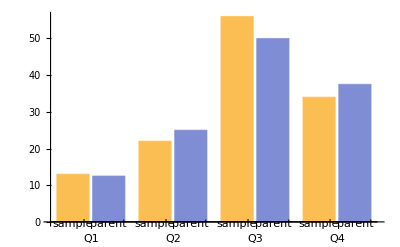

```mathematica
BarChart[Transpose[{accumulator,expected}],ChartLabels->{unitSalesByQuarterInMillions[[All,1]],{"sample","parent"}}]
```